```mathematica
Clear[F,G,p,R,Cost];
F[a_,k_]:=F[a,k]=Piecewise[{{1-∑_(n=0)^(k-1) 1/(n!)*(a/μ)^n*Exp[-a/μ], a>0}, {0, a==0}}];
p[a_,k_,j_]:=p[a,k,j]=Piecewise[{{Boole[j==k+1], a==0}, {Boole[j==1], a>0&&k==0}, {F[a,k], a>0&&k≥1&&j==1}, {F[a,k-j+1]-F[a,k-j+2], a>0&&k≥1&&2≤j&&j≤k}, {1-F[a,1], a>0&&k≥1&&j==(k+1)}, {0, True}}];
G[a_,k_]:=G[a,k]=Piecewise[{{μ*k*F[a,k+1]/F[a,k], a>0}, {0, a==0}}];
R[a_,k_,j_]:=R[a,k,j]=Piecewise[{{0, a==0}, {cI*a+(G[a,k]*(cW*(k+1)-2*cI))/2, a>0&&k≥0&&j==1}, {cW*a*(j-1)+(cW*G[a,k-j+1]*(k-j+2))/2, a>0&&k≥1&&2≤j&&j≤(k+1)}}];
Cost[a_,n_,k_]:=Cost[a,n,k]=∑_(j=1)^(k+1) p[a,k,j]*(R[a,k,j]+OptimalCost[n-1,j]);
```

```mathematica
Clear[PossiblePolicies];
PossiblePolicies[n_,k_]:=PossiblePolicies[n,k]=Module[{sol,result},
sol=NSolve[D[Cost[a,n,k],a]==0&&a>0,a]//Quiet;
If[Length[sol]==0,
result={0},
result=Flatten[{0,a/.sol}];
];
result
];
```

```mathematica
Clear[OptimalPolicy];
OptimalPolicy[n_,k_]:=OptimalPolicy[n,k]=Module[{a, costMin,i,result},
a=PossiblePolicies[n,k];
costMin=Min[Table[Cost[a[[i]],n,k],{i,1,Length[a]}]];
For[i=1,i≤Length[a],i++,
If[Cost[a[[i]],n,k]==costMin,
result=a[[i]];
];
];
result
];
```

```mathematica
Clear[OptimalCost];
OptimalCost[n_,k_]:=OptimalCost[n,k]=Piecewise[{{(cW*μ*k*(k+1))/2, n==0}, {Cost[OptimalPolicy[n,k],n,k], n≥1}}];
```

```mathematica
μ=1;
cW=1;
cI=1;
```

```mathematica
num=6;
Table[OptimalCost[n,0],{n,0,num}]
Table[Table[If[n+k≤num,OptimalCost[n,k],0],{k,0,num}],{n,0,num}]//MatrixForm
Table[Table[If[n+k≤num,OptimalPolicy[n,k],0],{k,0,num}],{n,1,num}]//MatrixForm
```

{0,1,2.69315,4.52005,6.35018,8.18013,10.0101}

(0 | 1 | 3 | 6 | 10 | 15 | 21
1 | 2.69315 | 4.97937 | 8.04949 | 11.9605 | 16.7418 | 0
2.69315 | 4.52005 | 6.81367 | 9.88121 | 13.7875 | 0 | 0
4.52005 | 6.35018 | 8.64338 | 11.7105 | 0 | 0 | 0
6.35018 | 8.18013 | 10.4733 | 0 | 0 | 0 | 0
8.18013 | 10.0101 | 0 | 0 | 0 | 0 | 0
10.0101 | 0 | 0 | 0 | 0 | 0 | 0)

(0 | 0.693147 | 1.75711 | 2.82577 | 3.85505 | 4.8492 | 0
0 | 0.826902 | 1.90223 | 2.95223 | 3.95872 | 0 | 0
0 | 0.83013 | 1.90481 | 2.95403 | 0 | 0 | 0
0 | 0.82995 | 1.90455 | 0 | 0 | 0 | 0
0 | 0.829925 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
TeXForm[MatrixForm[Table[Table[If[n+k≤num,OptimalCost[n,k],0],{k,0,num}],{n,0,num}]]]
```

\left(
\begin{array}{ccccccc}
 0 & 1 & 3 & 6 & 10 & 15 & 21 \\
 1 & 2.69315 & 4.97937 & 8.04949 & 11.9605 & 16.7418 & 0 \\
 2.69315 & 4.52005 & 6.81367 & 9.88121 & 13.7875 & 0 & 0 \\
 4.52005 & 6.35018 & 8.64338 & 11.7105 & 0 & 0 & 0 \\
 6.35018 & 8.18013 & 10.4733 & 0 & 0 & 0 & 0 \\
 8.18013 & 10.0101 & 0 & 0 & 0 & 0 & 0 \\
 10.0101 & 0 & 0 & 0 & 0 & 0 & 0 \\
\end{array}
\right)

```mathematica
TeXForm[MatrixForm[Table[Table[If[n+k≤num,OptimalPolicy[n,k],0],{k,0,num}],{n,1,num}]]]
```

\left(
\begin{array}{ccccccc}
 0 & 0.693147 & 1.75711 & 2.82577 & 3.85505 & 4.8492 & 0 \\
 0 & 0.826902 & 1.90223 & 2.95223 & 3.95872 & 0 & 0 \\
 0 & 0.83013 & 1.90481 & 2.95403 & 0 & 0 & 0 \\
 0 & 0.82995 & 1.90455 & 0 & 0 & 0 & 0 \\
 0 & 0.829925 & 0 & 0 & 0 & 0 & 0 \\
 0 & 0 & 0 & 0 & 0 & 0 & 0 \\
\end{array}
\right)

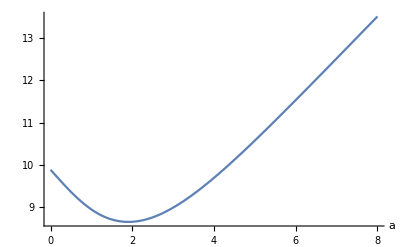

```mathematica
Plot[Cost[a,3,2],{a,0,8},AxesLabel->Automatic]
```

```mathematica
Cost[a,3,2]//FullSimplify
```

Piecewise[{{0., a<0}, {9.88121, a==0}, {(ⅇ^-a (-4.36117+(-3.29362-0.5 a) a-1.15888 ⅇ^a+(2.29362-0.5 a) a ⅇ^a+(5.52005+1. a) ⅇ^(2 a)))/(-1.+ⅇ^a), True}}]

```mathematica
TeXForm[FullSimplify[Cost[a,3,2]]]
```

\begin{cases}
 0. & a<0 \\
 9.88121 & a=0 \\
 \frac{e^{-a} \left(e^a a (2.29362\, -0.5 a)+(-0.5 a-3.29362) a-1.15888 e^a+(1. a+5.52005) e^{2 a}-4.36117\right)}{e^a-1.} & \text{True}
\end{cases}

```mathematica
PossiblePolicies[3,2]
OptimalPolicy[3,2]
OptimalCost[3,2]
```

{0,1.90481}

1.90481

8.64338